```mathematica
VertexCount[plantri8]
```

17

```mathematica
Length[plantri]
```

100000

```mathematica
2*(17-1)-5
```

27

```mathematica
(3n-6)/.n->27
```

75

```mathematica
pl=ReadPlantri["D:\\cygwin64\\home\\alfre\\five-75-edges.txt"];Length[pl]
```

329824

```mathematica
(*Put[pl,"d:\\saved\\plantribig.m"]//Timing*)
```

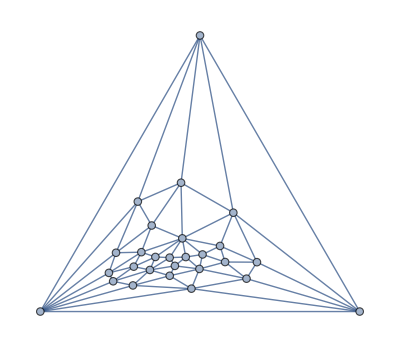

```mathematica
Graph[pl[[1]], GraphLayout->"TutteEmbedding"]
```

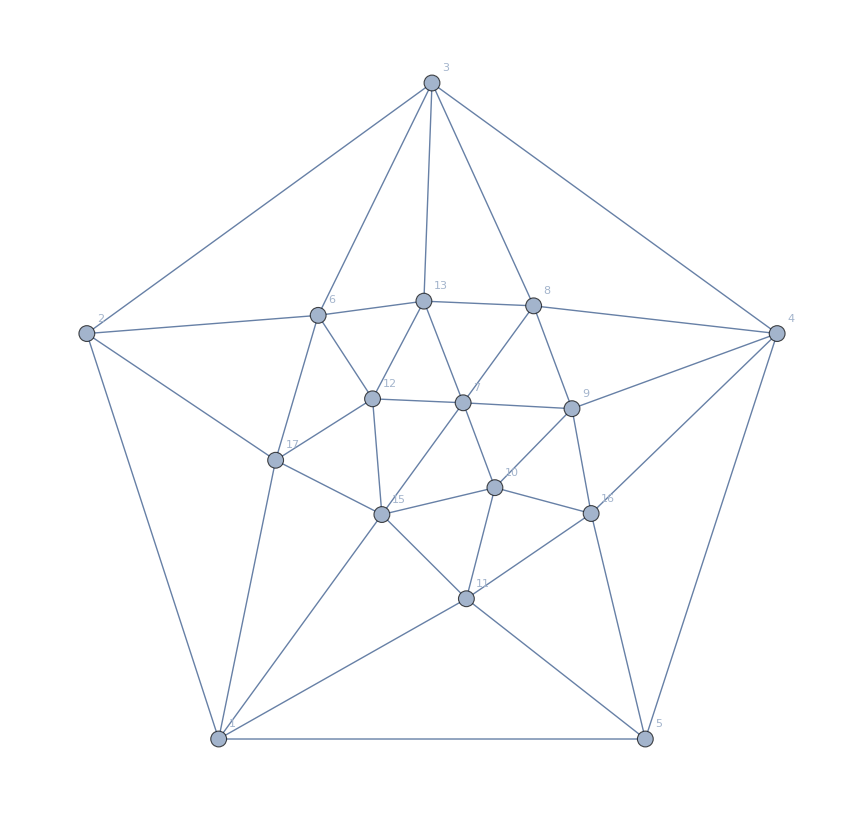

```mathematica
g=VertexDelete[Graph[plantri8, GraphLayout->"TutteEmbedding"],14]
```

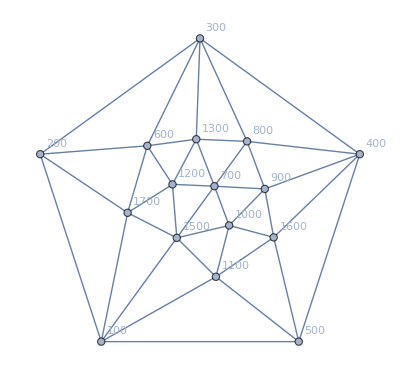

```mathematica
g2=Graph[VertexList[g]*100,Map[UndirectedEdge[#[[1]]*100,#[[2]]*100]&,EdgeList[g]], GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

```mathematica
EdgeList[g]
```

{12<->13,12<->7,12<->15,12<->17,12<->6,13<->6,13<->3,13<->8,13<->7,7<->8,7<->9,7<->10,7<->15,15<->10,15<->11,15<->1,15<->17,17<->1,17<->2,17<->6,6<->2,6<->3,3<->2,3<->4,3<->8,8<->4,8<->9,9<->4,9<->16,9<->10,10<->16,10<->11,11<->16,11<->5,11<->1,1<->5,1<->2,4<->5,4<->16,16<->5}

EdgeDelete::inv: The argument {2<->3,3<->4,4<->5,5<->6,6<->2} in EdgeDelete[Graph[<16>, <40>], {2 <-> 3, 3 <-> 4, 4 <-> 5, 5 <-> 6, 6 <-> 2}] is not a valid edge.

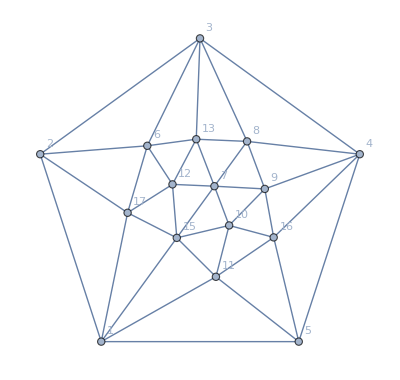
EdgeDelete[-Graphics-,{2<->3,3<->4,4<->5,5<->6,6<->2}]

```mathematica
EdgeDelete[g,{2<->3,3<->4,4<->5,5<->6,6<->2}]
```

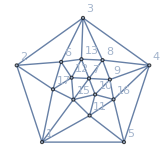
```mathematica
EdgeDelete[-Graphics-,{2<->3,3<->4,4<->5,5<->1,1<->2}]
```

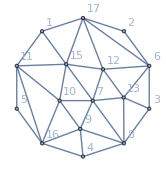

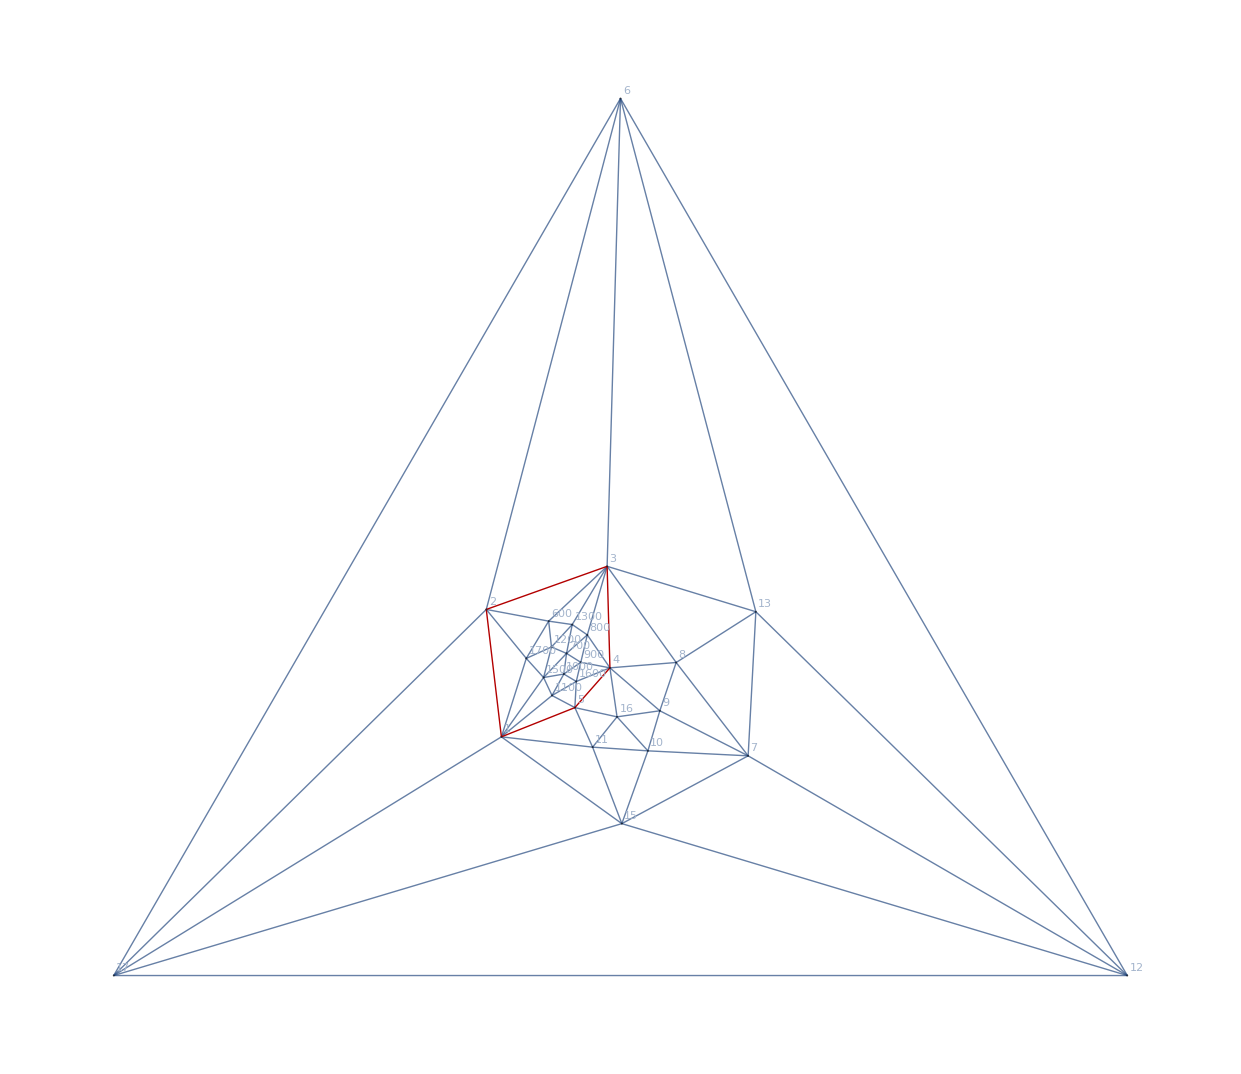

```mathematica
g3=VertexContract[VertexContract[VertexContract[VertexContract[VertexContract[GraphUnion[EdgeDelete[g,{2<->3,3<->4,4<->5,5<->1,1<->2}],g2],{1,100}],{2,200}],{3,300}],{4,400}],{5,500},GraphLayout->"TutteEmbedding", VertexLabels->"Name", VertexSize->Tiny, GraphHighlight->{2<->3,3<->4,4<->5,5<->1,1<->2}, GraphHighlightStyle->"Thick"]
```

```mathematica
EdgeCount[g3]
```

75

```mathematica
MaximalPlanarQ[g3]
```

True

```mathematica
Monitor[Select[Range[Length[pl]],Block[{k=#},IsomorphicGraphQ[Graph[pl[[#]]],g3]]&],k]
```

{183773}

```mathematica
ApplyPattern[g_,patt_]:=Block[{vertices=Select[patt,Length[#]==2&], result=g},
Table[result=VertexContract[result,s],{s,vertices}];
result
]
```

```mathematica
Table[allGraphs5[k,"colofour"],{k,alfa1s}]
```

{v13x24x5,v14x25x3,v1x24x35,v13x25x4,v14x2x35}

```mathematica
Table[ApplyPattern[g3,SymbolToSets[triangle]],{triangle,Table[allGraphs5[k,"colofour"],{k,alfa1s}]}]
```

{,,,,}

```mathematica
Monitor[Table[ChromaticPolynomial[ApplyPattern[g3,SymbolToSets[triangle]],4],{triangle,Table[allGraphs5[k,"colofour"],{k,alfa1s}]}],triangle]
```

{216,1536,0,1536,216}

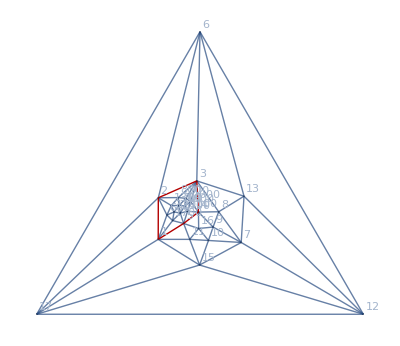

```mathematica
g4=VertexContract[VertexContract[VertexContract[VertexContract[VertexContract[GraphUnion[EdgeDelete[g,{2<->3,3<->4,4<->5,5<->1,1<->2}],g2],{1,200}],{2,300}],{3,400}],{4,500}],{5,100},GraphLayout->"TutteEmbedding", VertexLabels->"Name", VertexSize->Tiny, GraphHighlight->{2<->3,3<->4,4<->5,5<->1,1<->2}, GraphHighlightStyle->"Thick"]
```

```mathematica
Monitor[Table[ChromaticPolynomial[ApplyPattern[g4,SymbolToSets[triangle]],4],{triangle,Table[allGraphs5[k,"colofour"],{k,alfa1s}]}],triangle]
```

{0,1536,0,576,576}